```mathematica
(*
Variables
PER: Conc. of the non-phosphorylated PER,
PERP: Conc. of the prime-phosphorylated PER,
PERPP: Conc. of the hyperphosphorylated PER,
C1: Conc. of the PER-CK1 complex, 
C2: Conc. of the PERP-CK1 complex,
C3: Conc. of the PERP-PP1 complex,
C4: Conc. of the PERPP-PP1 complex,
CK1: Conc. of the CK1d/e,
PP1: Conc. of the PP1,
*)

(*Parameters*)
(*See Table S2 for the detailed description of the parameters*)
a1=0.0032; a2=0.016; a3=0.016; a4=0.0256;

d1=10; d2=5;  d3=0.5; d4=0.5;

k1=0.011; k2=0.15; k3=0.1; k4=0.05;

CK1tot=31250; PP1tot=7812.5;

(*Calculation of the steay state fractions of the hyperphopsrylated PER*)
f1[xo_]:=Module[{PERtot=xo},
equation=NSolve[

(*Equation*)
-a1*PER*CK1+d1*C1+k3*C3==0&&
k1*C1-a2*PERP*CK1+d2*C2-a3*PERP*PP1+d3*C3+k4*C4==0&&
k2*C2-a4*PERPP*PP1+d4*C4==0&&
a1*PER*CK1-(d1+k1)*C1==0&&
a2*PERP*CK1-(d2+k2)*C2==0&&
a3*PERP*PP1-(d3+k3)*C3==0&&
a4*PERPP*PP1-(d4+k4)*C4==0&&
PERtot-(PER+PERP+PERPP+C1+C2+C3+C4)==0&&
CK1tot-(CK1+C1+C2)==0&&
PP1tot-(PP1+C3+C4)==0&&
PER≥ 0&&PERP≥ 0&&PERPP≥ 0&&C1≥ 0&&C2≥ 0&&C3≥ 0&&C4≥ 0&&CK1≥ 0&&PP1≥ 0,

{PER,PERP,PERPP,C1,C2,C3,C4,CK1,PP1},Reals];

data={};
For[i=1,i<Dimensions[equation][[1]]+1,i++,
data=Join[data,{{PERtot,((PERPP+C4)/.equation[[i]])/PERtot}}];
];
data
];

range1=0.1;
range2=33000;
data=Table[f1[xtot],{xtot,range1,range2,0.005*range2}];

(*Classifiation of the steay state fractions to low branach, intermediate branch and upper branch to draw the graphs below*)
low1=Table[If[Dimensions[data[[i]]][[1]]==1&&data[[i]][[1]][[2]]<0.5,data[[i]][[1]],""],{i,1,Dimensions[data][[1]]}];
low2=Table[If[Dimensions[data[[i]]][[1]]==2&&data[[i]][[1]][[2]]<0.5,data[[i]][[1]],""],{i,1,Dimensions[data][[1]]}];
low3=Table[If[Dimensions[data[[i]]][[1]]==3,data[[i]][[Position[Transpose[data[[i]]][[2]],Min[Transpose[data[[i]]][[2]]]][[1]][[1]]]],""],{i,1,Dimensions[data][[1]]}];

inter1=Table[If[Dimensions[data[[i]]][[1]]==2&&data[[i]][[1]][[2]]<0.5,data[[i]][[2]],""],{i,1,Dimensions[data][[1]]}];
inter2=Table[If[Dimensions[data[[i]]][[1]]==3,data[[i]][[DeleteCases[DeleteCases[{1,2,3},Position[Transpose[data[[i]]][[2]],Min[Transpose[data[[i]]][[2]]]][[1]][[1]]],Position[Transpose[data[[i]]][[2]],Max[Transpose[data[[i]]][[2]]]][[1]][[1]]][[1]]]],""],{i,1,Dimensions[data][[1]]}];

upper1=Table[If[Dimensions[data[[i]]][[1]]==1&&data[[i]][[1]][[2]]≥0.5,data[[i]][[1]],""],{i,1,Dimensions[data][[1]]}];
upper2=Table[If[Dimensions[data[[i]]][[1]]==2&&data[[i]][[2]][[2]]≥0.5,data[[i]][[2]],""],{i,1,Dimensions[data][[1]]}];
upper3=Table[If[Dimensions[data[[i]]][[1]]==3,data[[i]][[Position[Transpose[data[[i]]][[2]],Max[Transpose[data[[i]]][[2]]]][[1]][[1]]]],""],{i,1,Dimensions[data][[1]]}];

lowbranch=Sort[DeleteCases[Join[low1,low2,low3],""],#1[[1]]<#2[[1]]&];
intermediate=Sort[DeleteCases[Join[inter1,inter2],""],#1[[1]]<#2[[1]]&];
upperbranch=Sort[DeleteCases[Join[upper1,upper2,upper3],""],#1[[1]]<#2[[1]]&];
```

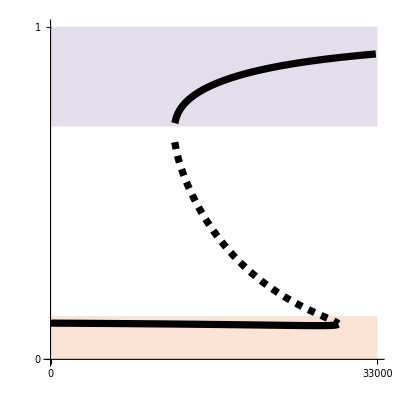
-Graphics-Local PER conc.(1/Ω)(Local hyperphos .  PER conc.)/(Local PER conc.)

```mathematica
(*Plotting the Graph*)

pthick=10^-2*1.3;
athick=10^-3;
ft=20;
red=RGBColor[236/255,28/255,36/255];

tick1={{{0,0,{0,0.017}},{range2/2,,{0,0.017}},{range2,range2,{0,0.017}}},{{0,0,{0,0.017}},{0.5,,{0,0.017}},{1,1,{0,0.017}}}};

frame=ListPlot[{{0.1,0.5}},PlotRange->{{0,range2},{0,1}},PlotStyle->Directive[White,Thickness[pthick]],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

lowbranchgraph=ListPlot[lowbranch,PlotRange->{{0,range2},{0,1}},PlotStyle->Directive[Black,Thickness[pthick]],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

intermediategraph=ListPlot[intermediate,PlotRange->{{0,range2},{0,1}},PlotStyle->Directive[Black,Thickness[pthick],Dashed],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

upperbranchgraph=ListPlot[upperbranch,PlotRange->{{0,range2},{0,1}},PlotStyle->Directive[Black,Thickness[pthick]],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

opa=0.2;
hypo=RGBColor[236/255,124/255,52/255];
hyper=RGBColor[124/255,92/255,164/255];

hypog=Graphics[{Directive[hypo,Opacity[opa]],Rectangle[{0,0},{range2,0.13}]}];
hyperg=Graphics[{Directive[hyper,Opacity[opa]],Rectangle[{0,0.7},{range2,1}]}];

Labeled[Show[frame,hypog,hyperg,lowbranchgraph,intermediategraph,upperbranchgraph],{"Local PER conc.(1/Ω)","(Local hyperphos .  PER conc.)/(Local PER conc.)"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica",ft}]
```

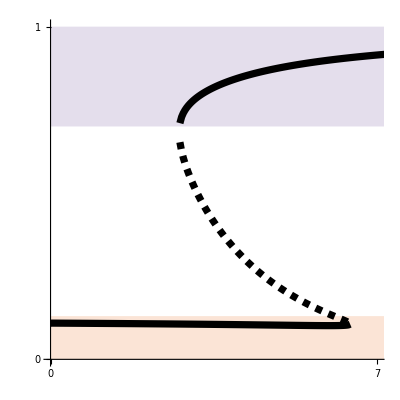
-Graphics-Norm. local PER conc.(Local hyperphos .  PER conc.)/(Local PER conc.)

```mathematica
(*Plotting the graph with the normalized PER conccentration (i.e. normalized x-axis)*)

(*PER concentration was normalized by the peak level of total PER concentration in Fig 3E*)

maxlevel=4527 (*the peak level of total PER in a normal cell in Fig 3E*);

pthick=10^-2*1.3;
athick=10^-3;
ft=20;
red=RGBColor[236/255,28/255,36/255];

tick1={{{0,0,{0,0.017}},{3.5,,{0,0.017}},{7,7,{0,0.017}}},{{0,0,{0,0.017}},{0.5,,{0,0.017}},{1,1,{0,0.017}}}};

frame=ListPlot[{{0.1,0.5}},PlotRange->{{0,7},{0,1}},PlotStyle->Directive[White,Thickness[pthick]],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

lowbranchgraph=ListPlot[Transpose[{Transpose[lowbranch][[1]]/maxlevel,Transpose[lowbranch][[2]]}],PlotRange->{{0,7.3},{0,1}},PlotStyle->Directive[Black,Thickness[pthick]],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

intermediategraph=ListPlot[Transpose[{Transpose[intermediate][[1]]/maxlevel,Transpose[intermediate][[2]]}],PlotRange->{{0,7.3},{0,1}},PlotStyle->Directive[Black,Thickness[pthick],Dashed],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

upperbranchgraph=ListPlot[Transpose[{Transpose[upperbranch][[1]]/maxlevel,Transpose[upperbranch][[2]]}],PlotRange->{{0,7.3},{0,1}},PlotStyle->Directive[Black,Thickness[pthick]],AxesStyle->Directive[Thickness[athick],FontSize->ft],BaseStyle->{FontFamily->"Helvetica",FontSize->ft},Ticks->tick1,TicksStyle->Directive[Black],AspectRatio->1,Joined->True];

opa=0.2;

hypo=RGBColor[236/255,124/255,52/255];
hyper=RGBColor[124/255,92/255,164/255];

hypog=Graphics[{Directive[hypo,Opacity[opa]],Rectangle[{0,0},{range2,0.13}]}];
hyperg=Graphics[{Directive[hyper,Opacity[opa]],Rectangle[{0,0.7},{range2,1}]}];

Labeled[Show[frame,hypog,hyperg,lowbranchgraph,intermediategraph,upperbranchgraph],{"Norm. local PER conc.","(Local hyperphos .  PER conc.)/(Local PER conc.)"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica",ft}]
```